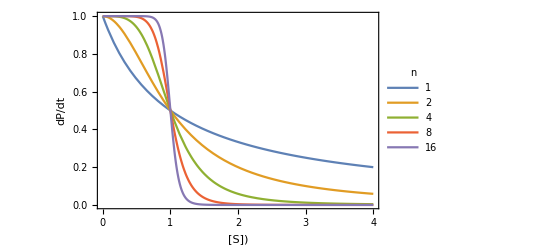

```mathematica
f[k_,n_,x_]:=(1)/(1+(x/k)^n)
r=PowerRange[1,16,2];
ex=f[1,#,x]&/@r;
Plot[ex,{x,0,4},PlotLegends->LineLegend[Automatic,r,LegendLabel->"n"],Frame->True,FrameLabel->{"[S])","dP/dt"}]
```